# Modeling Hurricane Velocity Field by Vector Decomposition

## Brayden Mi, Diane Guo Multivariable Calculus - G Carrier Dr. Raulston Authored by Brayden Mi

### Introduction

Understanding the velocity field distribution is an important component in assessing the strength and potential damage in hurricane research.  Modeling a realistic velocity field distribution is fundamental to subsequent hurricane research such as lateral and vertical mass flow with the the hurricane.  This project is an effort of modeling a hurricane velocity field by decomposing the vector field into various simpler components. The overall velocity field can then be obtained by superimposing of these simpler fields.  This process will be demonstrated with Mathematica.

### Simulating 2D Projection of Hurricane Velocity Field

#### Modeling Velocity Vector Field

We first begin by finding a vector field that represents the XY plane projection of the 3D velocity field.  A typical hurricane velocity field, for example, Katrina that raged along the coast of Louisiana in 2005, has a velocity contour plot shown below, where the fastest winds occur towards the center of the hurricane. 
-Graphics-
Note that the wind speed increase towards the center of the hurricane,  and the velocity field is not simple rotational vector, but has two components.  

The first component is the inwards movement towards the eye. Knowing that <x,y> represents an outwards expanding vector field (source flow),  the vector field can be multiplied by a scalar value of -1 to achieve <-x,-y>, which is the opposite behavior that points inwards (sink flow).

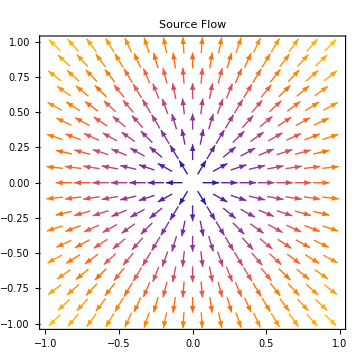
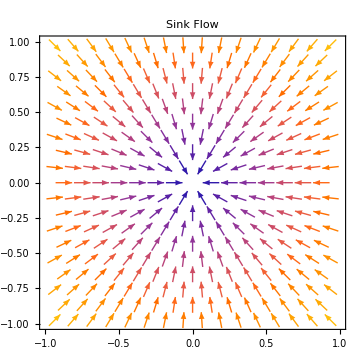

```mathematica
vectorFieldOUT = {q*x/(2*Pi),q*y/(2*Pi)};
vectorFieldIN = vectorFieldOUT*-1;
q = (2*Pi);
vectorOutPlot = VectorPlot[vectorFieldOUT,{x,-1,1},{y,-1,1},ImageSize->Medium,PlotLabel->"Source Flow"];
vectorInPlot = VectorPlot[vectorFieldIN,{x,-1,1},{y,-1,1},ImageSize->Medium,PlotLabel->"Sink Flow"];
Row[{vectorOutPlot, vectorInPlot}]
```

The second component is the rotational behavior, otherwise known as a vortex field.

2 π

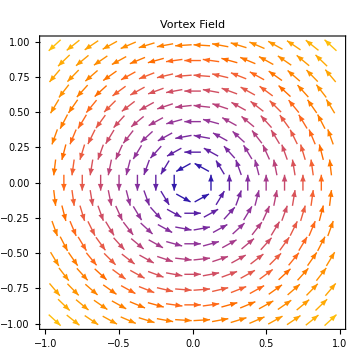

```mathematica
vectorRotation = {-k*y/(2*Pi),k*x/(2*Pi)};
k = (2*Pi)
vectorRotationPlot = VectorPlot[vectorRotation,{x,-1,1},{y,-1,1},ImageSize->Medium,PlotLabel->"Vortex Field"]
```

By combining these two components, we get an inwards (<-x,-y>) rotating (<-y,x>) spiral vector field, shown below.

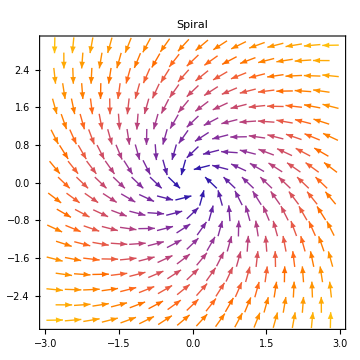

```mathematica
spiralVectors = vectorRotation + vectorFieldIN;
spiralVectorPlot = VectorPlot[spiralVectors,{x,-3,3},{y,-3,3},ImageSize->Medium,PlotLabel->"Spiral"]
```

However, this field is incorrect as the vector field depicts higher wind velocities (warmer toned arrows) towards the outer edges of the hurricane and slower wind velocities (cooler toned arrows) towards the center of the hurricane. This is corrected by multiplying the field with a 3D scalar function, which has an inverse relationship with the distance to the center of the hurricane. Note this function can be designed in different ways to simulate the velocity increase towards the center. Dividing by the distance formula of r^2 = x^2 + y^2 creates an inverse correlation for when radius increases, the velocity will decrease.

f(x,y) = (x^2+y^2);

This function weighs down the velocity field toward the edge the hurricane by the rotational radius.  The following code demonstrates the effect.

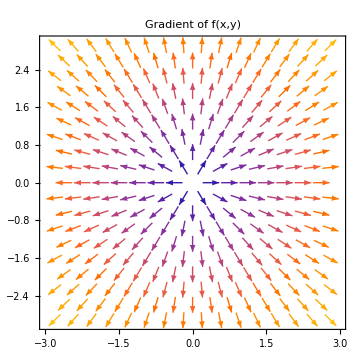
-Graphics3D--Graphics-

```mathematica
function = (x^2+y^2);
functionPlot = Plot3D[function,{x,-3,3},{y,-3,3},ImageSize->Medium, PlotLabel->"f(x,y) = (x^2+y^2)"];
functionGradient = Grad[function,{x,y}];
functionGradientPlot = VectorPlot[functionGradient,{x,-3,3},{y,-3,3},ImageSize->Medium,PlotLabel->"Gradient of f(x,y)"];
Row[{functionPlot,functionGradientPlot}]
```

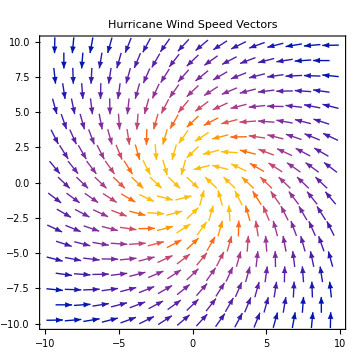
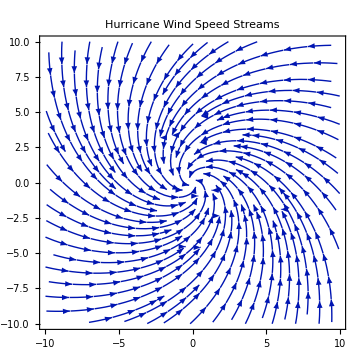

```mathematica
hurricaneVectors = spiralVectors/function;
hurricaneVectorPlot = VectorPlot[hurricaneVectors,{x,-10,10},{y,-10,10},ImageSize->Medium,PlotLabel->"Hurricane Wind Speed Vectors"];
hurricaneStreamPlot = StreamPlot[hurricaneVectors,{x,-10,10},{y,-10,10},ImageSize->Medium,PlotLabel->"Hurricane Wind Speed Streams"];
Row[{hurricaneVectorPlot,hurricaneStreamPlot}]
```

Additionally, a region function can be added to exclude a circle within the vector plot to  model the eye of the storm. This function can be modeled as circle function

r^2 = x^2 + y^2

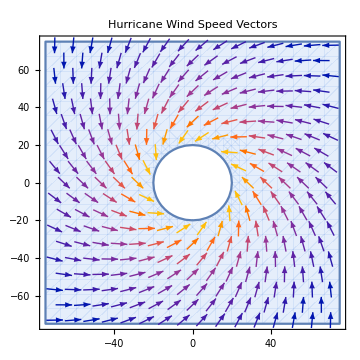

```mathematica
r=20;
eyePlot = VectorPlot[hurricaneVectors,{x,-75,75},{y,-75,75},ImageSize->Medium,PlotLabel->"Hurricane Wind Speed Vectors", RegionFunction->Function[{x,y},y^2>r^2-x^2]]
```

#### Modeling Air Pressure

It can be noted that the above velocity vector field, although resembles the overall air movement within a hurricane, it needs correction to simulate the eye of a hurricane, where the air pressure decreases to lowest at the eyewall and return to normal at some radius at the center (eye of the storm). This can be modeled through a contour plot defined as the slice of function 1/(x^2+y^2). The function for such would be A(x,y) (the dynamic radius) = p/-(x^2 + y^2) (function f(x,y)).

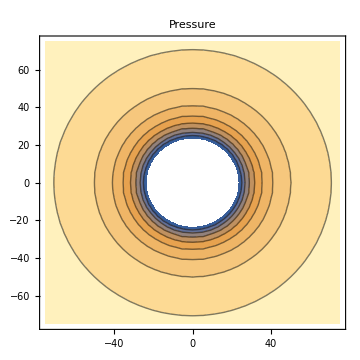

```mathematica
A[x_,y_]:=(p/-(x^2+y^2));
pressurePlot = ContourPlot[A[x,y]/.p->1,{x,-75,75},{y,-75,75}, ImageSize-> Medium, PlotLabel->"Pressure"]
```

When the hurricane plot is plotted with the pressure plot, the resulting graph looks like such:

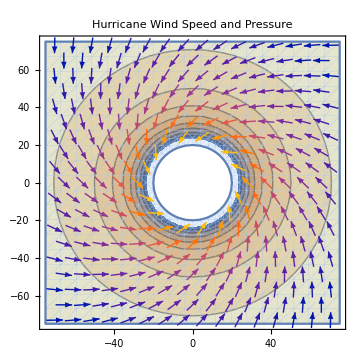

```mathematica
Show[{pressurePlot,eyePlot},ImageSize->Medium,PlotLabel->"Hurricane Wind Speed and Pressure"]
```

### Simulating 3D Projection of Hurricane Velocity Field

#### Modeling 3D Velocity Vector Field

The 3D version of the hurricane model can be achieved by adding a vertical velocity field to the above modeled 2D model.    For the vertical component, it can be assumed that the winds will rise at a speed of v/(x^2+y^2), which is an arbitrary constant divided by the same distance formula that the other vector components were divided by.  Note that this function can be altered to model different vertical movement. The resulting 3D vector field can be written as:

```mathematica
hurricaneVectors3DBase = {(-q*x-k*y)/(2*Pi*(x^2+y^2)),(k*x-q*y)/(2*Pi*(x^2+y^2)),v/(x^2+y^2)};
```

If it is assumed that k, q, and v are all equal to each other as a constant c, it can be factored out to be equal to 

c * <(-x-y)/(x^2+y^2), (x-y)/(x^2+y^2), 1/(x^2+y^2)>

To calculate for this proportionality constant as an example, we assume that the maximum velocity for wind is equal to 175 miles per hour (Katrina max velocity), and the radius of the eye is 20 miles (Average size of eye).

```mathematica
maxVelocity = 175;(*mph*)
radiusOfEye = 20; (*miles*)
c = maxVelocity/Sqrt[((-x-y)/(2*Pi*(x^2+y^2)))^2+((x-y)/(2*Pi*(x^2+y^2)))^2+(1/(x^2+y^2))^2]/.y->0/.x->Sqrt[radiusOfEye];
hurricaneVectors3D = c*{(-x-y)/(2*Pi*(x^2+y^2)),(x-y)/(2*Pi*(x^2+y^2)),1/(x^2+y^2)};
```

As shown in the following 3D vector field and the corresponding stream plot, velocity field spirals upwards, with increased velocity at the center, and increased stream at the edge.

```mathematica
hurricaneVectors3DPlot = VectorPlot3D[hurricaneVectors3D,{x,-150,150},{y,-150,150},{z,-150,150},ImageSize->Medium,AxesLabel->{"x","y","z"},PlotLabel->"3D Hurricane Vector Field", RegionFunction->Function[{x,y,z},z>-x^2-y^2+radiusOfEye^2]];
hurricaneStream3DPlot = StreamPlot3D[hurricaneVectors3D,{x,-150,150},{y,-150,150},{z,-150,150},ImageSize->Medium,AxesLabel->{"x","y","z"},PlotLabel->"3D Hurricane Stream Field",RegionFunction->Function[{x,y,z},z>-x^2-y^2+radiusOfEye^2]];
Row[{hurricaneVectors3DPlot,hurricaneStream3DPlot}]
```

-Graphics3D--Graphics3D-

Note that the velocity vector field of the fluid flow are tangent to the stream lines.  If the stream lines can be represented as the level curves of some scaler function ψ(x,y), ψ(x,y) is called a stream function for the flow.  The gradient of the stream function is normal to the level curves,  which implies ▽ψ•V=0, where V is the velocity field.

#### Particle Simulation of Vector Field

Particle simulation shows that fluid mass move into the hurricane at a slower velocity,  then accelerate towards the center and spiraling upwards (Linked Example). When slices are taken of the model, a clear eye of the storm and updraft can be seen on the X and Y axes (Linked Example X, Linked Example Y), and a swirl pattern can be seen on the Z slice (Linked Example Z). When looking at the streamlines and slices, the exact same thing can be seen (Linked Example, Linked Example X, Linked Example Y, Linked Example Z).

#### Calculating Flux of Vector Field across Ocean Surface

Assuming that the average hurricane diameter is 300 miles wide, we can calculate flux for the ocean surface at z = 0. This surface can be described as:

```mathematica
g=z;
bound=150^2-x^2-y^2;
ContourPlot3D[{g==0,bound==0},{x,-175,175},{y,-175,175},{z,0,175},MeshFunctions->{Function[{x,y,z,f},g-bound]},MeshStyle->{{Thin,Blue}},Mesh->{{0}},ContourStyle->{Directive[Orange,Opacity[0.5],Specularity[White,30]],Directive[Transparent,Opacity[0],Specularity[White,30]]},PlotPoints->60,SphericalRegion->True]
```

-Graphics3D-

Where the surface, g(x,y) = 0 is bounded by a circle of radius 150.

The 3D flux of the 3D hurricane vector field can then be calculated through the formula of Flux =  ∫∫_S F.nⅆS
. 
Because nⅆS = (∇g/||∇g||) * ||∇g||ⅆA, we can simplify nⅆS into ∇g ⅆA where g is surface.
Thus we can change our function to Flux = ∫∫_D F.∇gⅆA. 

When our values are plugged in for the surface g(x,y) = 0, bounded by curve x^2 + y^2 = 150^2 and subtracting the flux from the 20 mile radius eye,

c*(∫_-150^150 ∫_(-√(150^2-x^2))^(√(150^2-x^2))<(-x-y)/(x^2+y^2),(x-y)/(x^2+y^2),1/(x^2+y^2)>.∇gⅆyⅆx - ∫_-20^20 ∫_(-√(20^2-x^2))^(√(20^2-x^2))<(-x-y)/(x^2+y^2),(x-y)/(x^2+y^2),1/(x^2+y^2)>.∇gⅆyⅆx)

In polar coordinates
c∫_0^(2Pi) (∫_20)^150<(-rcos(T)-rsin(T))/((rcos(T))^2+(rsin(T))^2),(rcos(T)-rsin(T))/((rcos(T))^2+(rsin(T))^2),1/(((rcos(T))^2+(rsin(T))^2)>.∇g*rⅆrⅆT 
∇g = <0,0,1>

```mathematica
F = v*{(-x1-y1)/(2*Pi*(x1^2+y1^2)),(x1-y1)/(2*Pi*(x1^2+y1^2)),1/(x1^2+y1^2)}; 
x1=r*Cos[T]; (*Convert to polar*)
y1 = r*Sin[T]; (*Conver to polar*)
integrand = Dot[F,{0,0,1}]*radius;
TIntegral = Integrate[integrand,{T,0,2*Pi}];
rIntegral = Integrate[TIntegral,{radius,20,150}];
Flux = N[rIntegral];
Print[Flux" miles^3/hour"];
```

173.573  miles^3/hour

The hurricane for max velocity of 175 mph and eye radius of 20 miles and full radius of 150 sucks 173.573 cubic miles of air per hour.
Assuming that the amount of water present in 1 cubic mile of a hurricane is 2.08*10^6 kilograms per cubic mile, the amount of mass (water) within a 150 mile radius is

```mathematica
density = 2.08*10^6;
FluxofWater = Flux*density*0.001;
Print[FluxofWater " metric tonnes per hour"]
```

361032.  metric tonnes per hour